```mathematica
Remove["Global`*"];
```

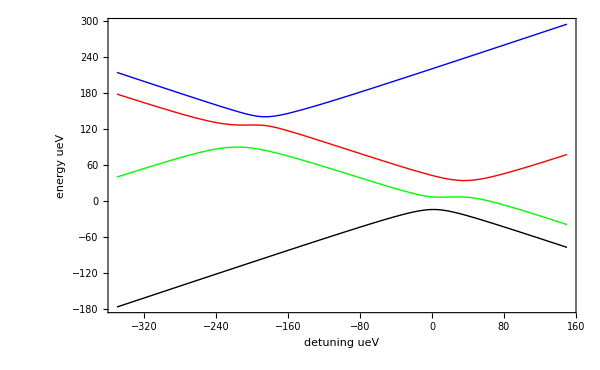

```mathematica
H=({{ϵ/2, 0, g1, -g2}, {0, ϵ/2+δl, -g3, g4}, {g1, -g3, -ϵ/2, 0}, {-g2, g4, 0, -ϵ/2+δr}});
(* basis states L0, L1, R0, R1 *)

h=4.135667516;


g1=2.62*h; (* frequency 2.62 GHz ; coupling between L0 and R0 *)
g2=3.5*h; (* frequency 3.5 GHz ; coupling between L1 and R0 *)
g3=4.6*h; (* frequency 4.6 GHz ; coupling between L0 and R1 *)
g4=1.85*h; (* frequency 1.85 GHz ; coupling between L1 and R1 *)
δl=218; (* left dot ST splitting 218 μeV *)
δr=38; (* right dot ST splitting 28 μeV *)

evals=Eigenvalues[H];
Plot[{evals[[1]],evals[[2]],evals[[3]],evals[[4]]},{ϵ,-350,150},PlotStyle->{{Black,Thick},{Green,Thick},{Red,Thick},{Blue,Thick}},Frame->True,Axes->None,ImageSize->600,FrameLabel->{detuning (ueV),energy(ueV)}]
```